```mathematica
ClearAll["Global`*"];ClearAll["WKB`*"];
```

```mathematica
(*Off[FindRoot::precw];Off[FindRoot::lstol];*)
```

```mathematica
<<"WKB.m";
```

```mathematica
SetDirectory["/Users/bakhodir/Downloads/Telegram Desktop"];<<WKB.m
```

WKBFormula::shdw: Symbol WKBFormula appears in multiple contexts {WKB`,Global`}; definitions in context WKB` may shadow or be shadowed by other definitions.

```mathematica
ClearAll["Global`*"];
```

```mathematica
Needs["MaTeX`"];
```

```mathematica
MaTeX["\\omega"]
```

-Graphics-

```mathematica
Get["WKB.m"];
```

```mathematica
Context[WKBFormula]
```

WKB`

## Sample

```mathematica
f[r_]=1/(1-k)-2/r+λ/r Log[r/λ]; V[r_]=f[r]((l(l+1))/r^2+f'[r]/r+m^2);
```

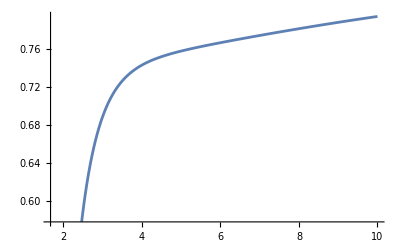

```mathematica
λ=0.000001;k=0.1;l=2;m=0.9;Plot[V[r],{r,1.67,10}]
```

```mathematica
Solve[1/(1-k)-2/r+λ/r Log[r/λ]==0/.{λ->0.2,k->0},r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→1.58588}}

```mathematica
Clear[λ]
```

```mathematica
Clear[l]
```

```mathematica
λ=0.1;m=0.2;k=0.;WKBFormula[V[r]/.{l->2},f[r],{r,2.34},0]
```

{0.579902-0.115225 ⅈ,0.579926-0.11522 ⅈ,0.579912-0.115149 ⅈ,0.579282-0.115274 ⅈ,0.580311-0.120335 ⅈ,0.608657-0.114731 ⅈ,r→2.68955}

```mathematica
rp[k_,λ_,l_,m_]:=r/.FindRoot[-1/((-1+k) r^5)(16-6 r+6 l r+6 l^2 r-2 l r^2-2 l^2 r^2+2 m^2 r^3+12 λ-4 r λ+l r λ+l^2 r λ+m^2 r^3 λ+λ^2-k (16+12 λ+λ^2+m^2 r^3 (2+λ)+l r (6+λ)+l^2 r (6+λ))-λ (16+3 (-1+l+l^2) r+m^2 r^3+6 λ-k (16+3 l r+3 l^2 r+m^2 r^3+6 λ)) Log[r/λ]-4 (-1+k) λ^2 Log[r/λ]^2)==0,{r,2}]
```

```mathematica
rp[0,0.2,2,0.2]
```

2.33958

```mathematica
<<MaTeX``
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
Clear[Omega6]
```

```mathematica
Clear[k,λ,l,m,n]
```

```mathematica
Omega6[k0_,lam0_,l0_,n0_,m0_]:=Module[{ff,vv,result,rguess},ff=f[r]/. {k->k0,λ->lam0};
vv=V[r]/. {k->k0,λ->lam0,l->l0,m->m0};
rguess=rp[k0,lam0,l0,m0];
result=WKBFormula[vv,ff,{r,rguess},n0];
First[result]]
Omega6[0.,0.1,2,0,0.2]
```

0.579902-0.115225 ⅈ

```mathematica
tab={};
Do[
Do[
w=WKBFormula[V[r]/.{l->1},f[r],{r,1.2},0][[4]];
If[TrueQ[w*Conjugate[w]<10],
tab=Append[tab,{ξ,m,w}];
];
,{ξ,0,3.99,0.1}];
,{m,0,0.5,0.05}];
tab2=Re[tab];tab3=Table[{tab[[i]][[1]],tab[[i]][[2]],Im[tab[[i]][[3]]]},{i,1,Dimensions[tab][[1]]}];
```

## New

```mathematica
fn[r_]:=1-2/r Exp[-a/r];Vn[r_]:=((l (1+l))/r^2+fn'[r]/r+(μ^2-m ω^2(1-(2a)/r^2))) (1-(2 ⅇ^(-a/r))/r);
```

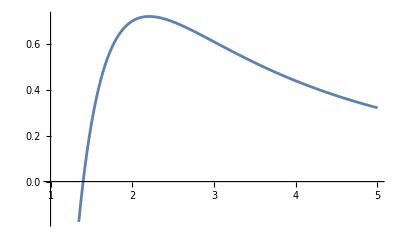

```mathematica
m=0.9;μ=0.1;ω=0.1;l=3;a=0.5;Plot[Vn[r],{r,1,5}]
```

```mathematica
Clear[l,m,a,μ,ω]
l=3;m=-3;a=0.5;μ=0.1;ω=0.1;WKBFormula[Vn[r],fn[r],{r,2.2},0][[1]]
```

0.843192-0.0981883 ⅈ

```mathematica
Clear[l]
```

```mathematica
tab={};
Do[
Do[
w=WKBFormula[Vn[r]/.{l->1},fn[r],{r,1},0][[1]];
If[TrueQ[w*Conjugate[w]<10],
tab=Append[tab,{ξ,m,w}];
];
,{ξ,0,3.99,0.1}];
,{m,0,0.5,0.05}];
tab2=Re[tab];tab3=Table[{tab[[i]][[1]],tab[[i]][[2]],Im[tab[[i]][[3]]]},{i,1,Dimensions[tab][[1]]}];
```

```mathematica
tab
```

```mathematica
Omega6[0.,0.1,2,0,0.2]
```

Omega6[0.,0.1,2,0,0.2]

```mathematica
WKBFormula[Vexpr[r,0.1,0.1,2,0.2],fexpr[r,0.1,0.1],{r,2.5},0]

WKBFormula[Vexpr[r,0.1,0.2,2,0.2],fexpr[r,0.1,0.2],{r,2.5},0]

WKBFormula[Vexpr[r,0.1,0.3,2,0.2],fexpr[r,0.1,0.3],{r,2.02593},0]
```

{0.684184-0.142071 ⅈ,0.68422-0.142064 ⅈ,0.684199-0.141961 ⅈ,0.683348-0.142138 ⅈ,0.684751-0.148733 ⅈ,0.72053-0.141347 ⅈ,r→2.29951}

{0.753256-0.162403 ⅈ,0.753308-0.162391 ⅈ,0.753278-0.162252 ⅈ,0.752195-0.162485 ⅈ,0.753974-0.170532 ⅈ,0.796078-0.161512 ⅈ,r→2.12292}

{0.803955-0.179405 ⅈ,0.804028-0.179389 ⅈ,0.803987-0.179205 ⅈ,0.802653-0.179503 ⅈ,0.804829-0.188997 ⅈ,0.852739-0.178378 ⅈ,r→2.02593}

```mathematica
ClearAll[Omega6];

Omega6[k0_?NumericQ,lam0_?NumericQ,ell0_Integer,n0_Integer,mass0_?NumericQ]:=Module[{ff,vv,rh,peak,rp,res},(*Metric function*)ff=fexpr[r,k0,lam0];
(*Effective potential*)vv=Vexpr[r,k0,lam0,ell0,mass0];
(*1. Event horizon*)rh=r/. FindRoot[ff==0,{r,2 (1-k0)}];
(*2. Physical potential maximum OUTSIDE the horizon*)peak=NMaximize[{vv,rh+10^-4<r<20},r];
rp=r/. peak[[2]];
(*3. Sixth-order WKB*)res=WKBFormula[vv,ff,{r,rp},n0];
(*First element=sixth-order WKB*)res[[1]]]
```

```mathematica
Omega6[0.,1,2,0,0.2]
Omega6[0.1,1,2,0,0.2]
Omega6[0.3,1,2,0,0.2]
```

0.780715-0.1944 ⅈ

0.872775-0.227924 ⅈ

1.14714-0.335119 ⅈ

```mathematica
<<MaTeX``
```

## freq vs k

```mathematica
fexpr[r_,k_,lam_]:=1/(1-k)-2/r+lam/r Log[r/lam];

Vexpr[r_,k_,lam_,ell_,mass_]:=fexpr[r,k,lam]*(ell (ell+1)/r^2+(D[fexpr[x,k,lam],x]/. x->r)/r+mass^2);


Omega6[k0_?NumericQ,lam0_?NumericQ,ell0_Integer,n0_Integer,mass0_?NumericQ]:=Module[{ff,vv,rh,peak,rp,res},(*Metric function*)ff=fexpr[r,k0,lam0];
(*Effective potential*)vv=Vexpr[r,k0,lam0,ell0,mass0];
(*1. Event horizon*)rh=r/. FindRoot[ff==0,{r,2 (1-k0)}];
(*2. Physical potential maximum OUTSIDE the horizon*)peak=NMaximize[{vv,rh+10^-4<r<20},r];
rp=r/. peak[[2]];
(*3. Sixth-order WKB*)res=WKBFormula[vv,ff,{r,rp},n0];
(*First element=sixth-order WKB*)res[[1]]]
```

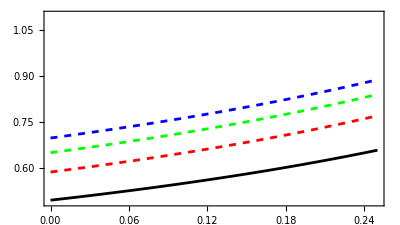

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/freqRe1.pdf

```mathematica
freqRe1=ListLinePlot[{Table[{k,Sqrt[1-k] Re[Omega6[k,10^-6,2,0,0.2]]},{k,0,0.25,0.01}],Table[{k,Sqrt[1-k] Re[Omega6[k,0.1,2,0,0.2]]},{k,0,0.25,0.01}],Table[{k,Sqrt[1-k] Re[Omega6[k,0.2,2,0,0.2]]},{k,0,0.25,0.01}],Table[{k,Sqrt[1-k] Re[Omega6[k,0.3,2,0,0.2]]},{k,0,0.25,0.01}]},FrameLabel->{MaTeX["k",Magnification->1.3],MaTeX["M\\omega_{R,\\infty}",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["\\lambda/M \\to 0",Magnification->1.3],MaTeX["\\lambda/M=0.1",Magnification->1.3],MaTeX["\\lambda/M=0.2",Magnification->1.3],MaTeX["\\lambda/M=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.5,0.8}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,Frame->True,PlotRange->{{0,.25},{0.49,1.1}}]

Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/freqRe1.pdf",freqRe1,"PDF"]
```

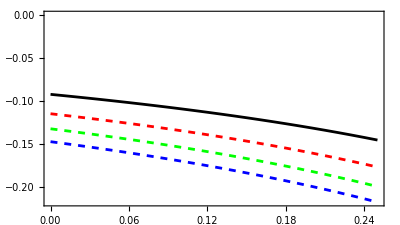

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/freqIm1.pdf

```mathematica
freqIm1=ListLinePlot[{Table[{k,Sqrt[1-k] Im[Omega6[k,10^-6,2,0,0.2]]},{k,0,0.25,0.01}],Table[{k,Sqrt[1-k] Im[Omega6[k,0.1,2,0,0.2]]},{k,0,0.25,0.01}],Table[{k,Sqrt[1-k] Im[Omega6[k,0.2,2,0,0.2]]},{k,0,0.25,0.01}],Table[{k,Sqrt[1-k] Im[Omega6[k,0.3,2,0,0.2]]},{k,0,0.25,0.01}]},FrameLabel->{MaTeX["k",Magnification->1.3],MaTeX["M\\omega_{I,\\infty}",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["\\lambda/M \\to 0",Magnification->1.3],MaTeX["\\lambda/M=0.1",Magnification->1.3],MaTeX["\\lambda/M=0.2",Magnification->1.3],MaTeX["\\lambda/M=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.5,0.8}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->All,Frame->True]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/freqIm1.pdf",freqIm1,"PDF"]
```

```mathematica
NMaximize[{Vexpr[r,0.1,0.3,2,0.2],r>1.3867&&r<10},r]
```

{0.695344,{r→2.02593}}

## freq vs λ

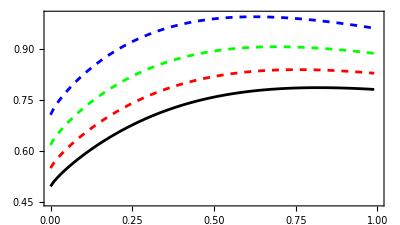

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/freqRe2.pdf

```mathematica
freqRe2=ListLinePlot[{Table[{λ,Re[Omega6[0,λ,2,0,0.2]]},{λ,10^-6,1,0.01}],Table[{λ,Sqrt[1-0.1] Re[Omega6[0.1,λ,2,0,0.2]]},{λ,10^-6,1,0.01}],Table[{λ,Sqrt[1-0.2]Re[Omega6[0.2,λ,2,0,0.2]]},{λ,10^-6,1,0.01}],Table[{λ,Sqrt[1-0.3]Re[Omega6[0.3,λ,2,0,0.2]]},{λ,10^-6,1,0.01}]},FrameLabel->{MaTeX["\lambda/M",Magnification->1.3],MaTeX["M\\omega_{R,\\infty}",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["k = 0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.2",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.6,0.2}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,1},{0.45,1}},Frame->True]

Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/freqRe2.pdf",freqRe2,"PDF"]
```

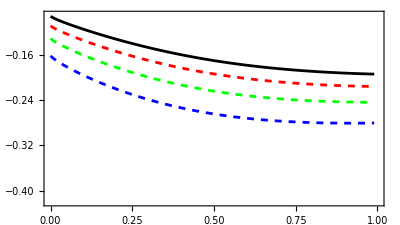

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/freqIm2.pdf

```mathematica
freqIm2=ListLinePlot[{Table[{λ,Im[Omega6[0,λ,2,0,0.2]]},{λ,10^-6,1,0.01}],Table[{λ,Sqrt[1-0.1]Im[Omega6[0.1,λ,2,0,0.2]]},{λ,10^-6,1,0.01}],Table[{λ,Sqrt[1-0.2]Im[Omega6[0.2,λ,2,0,0.2]]},{λ,10^-6,1,0.01}],Table[{λ,Sqrt[1-0.3]Im[Omega6[0.3,λ,2,0,0.2]]},{λ,10^-6,1,0.01}]},FrameLabel->{MaTeX["\lambda/M",Magnification->1.3],MaTeX["M\\omega_{I,\\infty}",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["k =0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.2",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.5,0.22}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,1},{-0.42,-0.09}},Frame->True]

Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/freqIm2.pdf",freqIm2,"PDF"]
```

## freq vs m

```mathematica
Omega6[0.1,10^-6,2,0,0.9]
Omega6[0.1,0.1,2,0,0.95]
Omega6[0.1,0.2,2,0,1]
Omega6[0.1,0.3,2,0,1]
```

```mathematica
ClearAll[WKBCheck];

WKBCheck[k0_?NumericQ,lam0_?NumericQ,ell0_Integer,n0_Integer,mass0_?NumericQ]:=Module[{ff,vv,rh,peak,rp,vmax,vinf,curvature,res,omega6},ff=fexpr[r,k0,lam0];
vv=Vexpr[r,k0,lam0,ell0,mass0];
(*Event horizon*)rh=r/. FindRoot[ff==0,{r,2 (1-k0)}];
(*Physical barrier maximum outside horizon*)peak=NMaximize[{vv,rh+10^-4<r<20},r];
vmax=peak[[1]];
rp=r/. peak[[2]];
(*Asymptotic plateau*)vinf=mass0^2/(1-k0);
(*Second derivative with respect to tortoise coordinate*)curvature=(fexpr[r,k0,lam0]^2*D[Vexpr[r,k0,lam0,ell0,mass0],{r,2}])/. r->rp;
(*WKB results*)res=WKBFormula[vv,ff,{r,rp},n0];
omega6=res[[1]];
{"rh"->rh,"rp"->rp,"Vmax"->vmax,"Vinf"->vinf,"Vmax-Vinf"->vmax-vinf,"VxxPeak"->curvature,"omega6"->omega6}]
```

```mathematica
WKBCheck[0.1,0.000001,2,0,0.7]//TableForm
```

rh→1.79999
rp→3.40426
Vmax→0.55421
Vinf→0.544444
Vmax-Vinf→0.00976533
VxxPeak→-0.0164164
omega6→0.719362-0.0592462 ⅈ

```mathematica
massValues=Range[0,0.7,0.1];

Table[{m,WKBCheck[0.1,0.1,2,0,m]},{m,massValues}]//TableForm
```

0. | rh→1.55314
rp→2.27677
Vmax→0.484232
Vinf→0.
Vmax-Vinf→0.484232
VxxPeak→-0.0847728
omega6→0.673839-0.145905 ⅈ
0.1 | rh→1.55314
rp→2.28237
Vmax→0.487941
Vinf→0.0111111
Vmax-Vinf→0.47683
VxxPeak→-0.084338
omega6→0.67642-0.14495 ⅈ
0.2 | rh→1.55314
rp→2.29951
Vmax→0.499185
Vinf→0.0444444
Vmax-Vinf→0.45474
VxxPeak→-0.0829788
omega6→0.684184-0.142071 ⅈ
0.3 | rh→1.55314
rp→2.32937
Vmax→0.518318
Vinf→0.1
Vmax-Vinf→0.418318
VxxPeak→-0.0805317
omega6→0.697191-0.137219 ⅈ
0.4 | rh→1.55314
rp→2.37415
Vmax→0.545956
Vinf→0.177778
Vmax-Vinf→0.368178
VxxPeak→-0.0767235
omega6→0.715546-0.130303 ⅈ
0.5 | rh→1.55314
rp→2.4377
Vmax→0.583017
Vinf→0.277778
Vmax-Vinf→0.30524
VxxPeak→-0.0711738
omega6→0.739404-0.121177 ⅈ
0.6 | rh→1.55314
rp→2.52684
Vmax→0.630797
Vinf→0.4
Vmax-Vinf→0.230797
VxxPeak→-0.0634048
omega6→0.768969-0.109606 ⅈ
0.7 | rh→1.55314
rp→2.65451
Vmax→0.691112
Vinf→0.544444
Vmax-Vinf→0.146667
VxxPeak→-0.0528613
omega6→0.804491-0.0952072 ⅈ

```mathematica
rp07=rp[0.1,0.1,2,0.9];

WKBFormula[Vexpr[r,0.1,0.1,2,0.9],fexpr[r,0.1,0.1],{r,rp07},0]//TableForm
```

0.859196-0.0421689 ⅈ
0.900585-0.0402309 ⅈ
0.901607-0.0588237 ⅈ
0.890354-0.0595672 ⅈ
0.890225-0.0576138 ⅈ
0.929848-0.0551588 ⅈ
r→3.20211

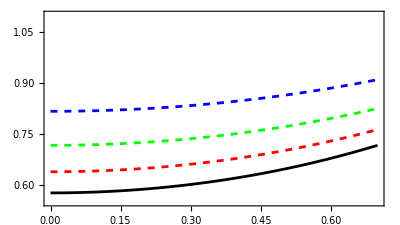

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mRealfreq1.pdf

```mathematica
mRealfreq1=ListLinePlot[{Table[{m,Re[Omega6[0.0,0.1,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.1]Re[Omega6[0.1,0.1,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.2]Re[Omega6[0.2,0.1,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.3]Re[Omega6[0.3,0.1,2,0,m]]},{m,0,0.7,0.01}]},Frame->True,FrameLabel->{MaTeX["mM",Magnification->1.3],MaTeX["M\\omega_{R,\infty}",Magnification->1.3],MaTeX["\\ell=2,\\; \\lambda=0.1,\\; n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.2",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.4,0.75}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0.,.7},{0.55,1.1}}]

Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mRealfreq1.pdf",mRealfreq1,"PDF"]
```

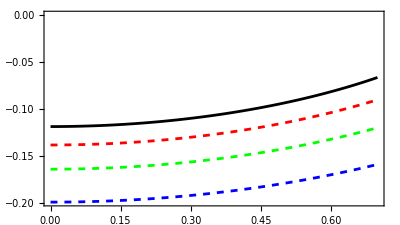

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mImagfreq1.pdf

```mathematica
mImagfreq1=ListLinePlot[{Table[{m,Im[Omega6[0.0,0.1,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.1]Im[Omega6[0.1,0.1,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.2]Im[Omega6[0.2,0.1,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.3]Im[Omega6[0.3,0.1,2,0,m]]},{m,0,0.7,0.01}]},Frame->True,FrameLabel->{MaTeX["mM",Magnification->1.3],MaTeX["M\\omega_{I,\infty}",Magnification->1.3],MaTeX["\\ell=2,\\; \\lambda/M=0.1,\\; n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.2",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.4,0.75}],{0.5,0.55}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->All]


Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mImagfreq1.pdf",mImagfreq1,"PDF"]
```

```mathematica
Omega6[0.1,0.1,2,0,0]
```

0.673839-0.145905 ⅈ

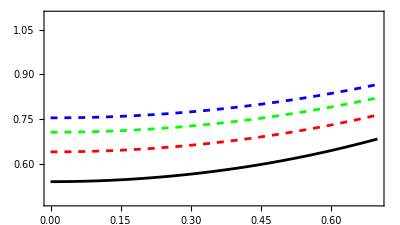

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mRealfreq2.pdf

```mathematica
mRealfreq2=ListLinePlot[{Table[{m,Sqrt[1-0.1]Re[Omega6[0.1,10^-6,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.1]Re[Omega6[0.1,0.1,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.1]Re[Omega6[0.1,0.2,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.1]Re[Omega6[0.1,0.3,2,0,m]]},{m,0,0.7,0.01}]},Frame->True,FrameLabel->{MaTeX["mM",Magnification->1.3],MaTeX["M\\omega_{R,\infty}",Magnification->1.3],MaTeX["\\ell=2,\\; k=0.1,\\; n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["\lambda/M \\to 0",Magnification->1.3],MaTeX["\lambda/M=0.1",Magnification->1.3],MaTeX["\lambda/M=0.2",Magnification->1.3],MaTeX["\lambda/M=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.5,0.8}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,0.7},{0.47,1.1}}]

Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mRealfreq2.pdf",mRealfreq2,"PDF"]
```

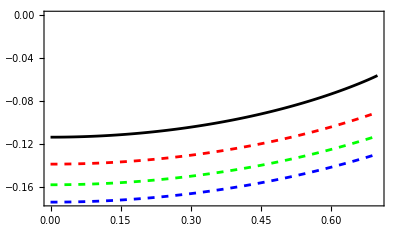

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mImagfreq2.pdf

```mathematica
mImagfreq2=ListLinePlot[{Table[{m,Sqrt[1-0.1]Im[Omega6[0.1,10^-6,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.1]Im[Omega6[0.1,0.1,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.1]Im[Omega6[0.1,0.2,2,0,m]]},{m,0,0.7,0.01}],Table[{m,Sqrt[1-0.1]Im[Omega6[0.1,0.3,2,0,m]]},{m,0,0.7,0.01}]},Frame->True,FrameLabel->{MaTeX["mM",Magnification->1.3],MaTeX["M\\omega_{I,\infty}",Magnification->1.3],MaTeX["\\ell=2,\\; k=0.1,\\; n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["\lambda/M \\to 0",Magnification->1.3],MaTeX["\lambda/M=0.1",Magnification->1.3],MaTeX["\lambda/M=0.2",Magnification->1.3],MaTeX["\lambda/M=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.4,0.72}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->All]


Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mImagfreq2.pdf",mImagfreq2,"PDF"]
```

## Comment requirement

```mathematica
resBenchmark=WKBFormula[Vexpr[r,0.0,0.1,2,0.2],fexpr[r,0.0,0.1],{r,rp[0.0,0.1,2,0.2]},0];

orders=Range[1,6];

omegaByOrder=Reverse[resBenchmark[[1;;6]]];

table1=Table[{orders[[i]],Re[omegaByOrder[[i]]],Im[omegaByOrder[[i]]]},{i,1,6}];

TableForm[table1,TableHeadings->{None,{"WKB order","Re[ω]","Im[ω]"}}]
```

WKB order | Re[ω] | Im[ω]
1 | 0.616224 | -0.114482
2 | 0.588496 | -0.119876
3 | 0.587524 | -0.115009
4 | 0.588122 | -0.114892
5 | 0.588135 | -0.11496
6 | 0.588113 | -0.114964

```mathematica
delta=Table[If[i==1,"-",Abs[omegaByOrder[[i]]-omegaByOrder[[i-1]]]/Abs[omegaByOrder[[i]]]],{i,1,6}];

tableConv=Table[{orders[[i]],Re[omegaByOrder[[i]]],Im[omegaByOrder[[i]]],delta[[i]]},{i,1,6}];

TableForm[tableConv,TableHeadings->{None,{"WKB order","Re[ω]","Im[ω]","δ_N"}}]
```

WKB order | Re[ω] | Im[ω] | δ_N
1 | 0.616224 | -0.114482 | -
2 | 0.588496 | -0.119876 | 0.0470346
3 | 0.587524 | -0.115009 | 0.00829066
4 | 0.588122 | -0.114892 | 0.00101677
5 | 0.588135 | -0.11496 | 0.000115283
6 | 0.588113 | -0.114964 | 0.0000381567

```mathematica
tableConvFormatted=tableConv/. x_Real:>NumberForm[x,{10,6}];

TableForm[tableConvFormatted,TableHeadings->{None,{"WKB order","Re[ω]","Im[ω]","δ_N"}}]
```

WKB order | Re[ω] | Im[ω] | δ_N
1 | 0.616224 | -0.114482 | Missing[NotAvailable]
2 | 0.588496 | -0.119876 | 0.047035
3 | 0.587524 | -0.115009 | 0.008291
4 | 0.588122 | -0.114892 | 0.001017
5 | 0.588135 | -0.114960 | 0.000115
6 | 0.588113 | -0.114964 | 0.000038

```mathematica
Omega6[0,0.1,2,0,0.2]
```

0.588113-0.114964 ⅈ

```mathematica
kValues={0,0.05,0.10,0.15,0.20,0.25};
lambdaValues={10^-6,0.1,0.2,0.3};

tableK=Flatten[Table[Module[{w},w=Omega6[k,lam,2,0,0.2];
{k,lam,Re[w],Im[w]}],{k,kValues},{lam,lambdaValues}],1];

TableForm[tableK/. x_Real:>NumberForm[x,{10,6}],TableHeadings->{None,{"k","λ","Re[ω6]","Im[ω6]"}}]
```

k | λ | Re[ω6] | Im[ω6]
0 | 1/1000000 | 0.496328 | -0.092397
0 | 0.100000 | 0.588113 | -0.114964
0 | 0.200000 | 0.651135 | -0.132494
0 | 0.300000 | 0.698978 | -0.147500
0.050000 | 1/1000000 | 0.535299 | -0.102909
0.050000 | 0.100000 | 0.632987 | -0.127466
0.050000 | 0.200000 | 0.698909 | -0.146310
0.050000 | 0.300000 | 0.748157 | -0.162262
0.100000 | 1/1000000 | 0.579902 | -0.115225
0.100000 | 0.100000 | 0.684184 | -0.142071
0.100000 | 0.200000 | 0.753256 | -0.162403
0.100000 | 0.300000 | 0.803955 | -0.179405
0.150000 | 1/1000000 | 0.631338 | -0.129781
0.150000 | 0.100000 | 0.743030 | -0.159284
0.150000 | 0.200000 | 0.815530 | -0.181309
0.150000 | 0.300000 | 0.867721 | -0.199485
0.200000 | 1/1000000 | 0.691155 | -0.147157
0.200000 | 0.100000 | 0.811231 | -0.179769
0.200000 | 0.200000 | 0.887473 | -0.203734
0.200000 | 0.300000 | 0.941181 | -0.223227
0.250000 | 1/1000000 | 0.761385 | -0.168132
0.250000 | 0.100000 | 0.891018 | -0.204416
0.250000 | 0.200000 | 0.971356 | -0.230620
0.250000 | 0.300000 | 1.026581 | -0.251597

```mathematica
lambdaValues2={10^-6,0.1,0.3,0.5,0.7,1.0};
kValues2={0,0.1,0.2,0.3};

tableLambda=Flatten[Table[Module[{w},w=Omega6[k,lam,2,0,0.2];
{lam,k,Re[w],Im[w]}],{lam,lambdaValues2},{k,kValues2}],1];

TableForm[tableLambda/. x_Real:>NumberForm[x,{10,6}],TableHeadings->{None,{"λ","k","Re[ω6]","Im[ω6]"}}]
```

λ | k | Re[ω6] | Im[ω6]
1/1000000 | 0 | 0.496328 | -0.092397
1/1000000 | 0.100000 | 0.579902 | -0.115225
1/1000000 | 0.200000 | 0.691155 | -0.147157
1/1000000 | 0.300000 | 0.844736 | -0.193774
0.100000 | 0 | 0.588113 | -0.114964
0.100000 | 0.100000 | 0.684184 | -0.142071
0.100000 | 0.200000 | 0.811231 | -0.179769
0.100000 | 0.300000 | 0.985358 | -0.234441
0.300000 | 0 | 0.698978 | -0.147500
0.300000 | 0.100000 | 0.803955 | -0.179405
0.300000 | 0.200000 | 0.941181 | -0.223227
0.300000 | 0.300000 | 1.126894 | -0.285910
0.500000 | 0 | 0.758730 | -0.170410
0.500000 | 0.100000 | 0.863574 | -0.204462
0.500000 | 0.200000 | 0.999481 | -0.250748
0.500000 | 0.300000 | 1.181744 | -0.316212
0.700000 | 0 | 0.783207 | -0.184781
0.700000 | 0.100000 | 0.883893 | -0.219289
0.700000 | 0.200000 | 1.013666 | -0.265830
0.700000 | 0.300000 | 1.186623 | -0.331099
1.000000 | 0 | 0.780715 | -0.194400
1.000000 | 0.100000 | 0.872775 | -0.227924
1.000000 | 0.200000 | 0.990787 | -0.272773
1.000000 | 0.300000 | 1.147140 | -0.335119

```mathematica
ClearAll[tableMassK];

mValues={0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8};
kValuesMass={0,0.1,0.2,0.3};

tableMassK=Flatten[Table[Module[{w},w=Omega6[k,0.1,2,0,m];
{m,k,Re[w],Im[w]}],{m,mValues},{k,kValuesMass}],1];

TableForm[tableMassK/. x_Real:>NumberForm[x,{10,6}],TableHeadings->{None,{"m","k","Re[ω6]","Im[ω6]"}}]
```

m | k | Re[ω6] | Im[ω6]
0 | 0 | 0.577127 | -0.118825
0 | 0.100000 | 0.673839 | -0.145905
0 | 0.200000 | 0.801571 | -0.183568
0 | 0.300000 | 0.976437 | -0.238193
0.100000 | 0 | 0.579867 | -0.117865
0.100000 | 0.100000 | 0.676420 | -0.144950
0.100000 | 0.200000 | 0.803983 | -0.182621
0.100000 | 0.300000 | 0.978665 | -0.237258
0.200000 | 0 | 0.588113 | -0.114964
0.200000 | 0.100000 | 0.684184 | -0.142071
0.200000 | 0.200000 | 0.811231 | -0.179769
0.200000 | 0.300000 | 0.985358 | -0.234441
0.300000 | 0 | 0.601945 | -0.110063
0.300000 | 0.100000 | 0.697191 | -0.137219
0.300000 | 0.200000 | 0.823362 | -0.174973
0.300000 | 0.300000 | 0.996546 | -0.229713
0.400000 | 0 | 0.621504 | -0.103047
0.400000 | 0.100000 | 0.715546 | -0.130303
0.400000 | 0.200000 | 0.840449 | -0.168164
0.400000 | 0.300000 | 1.012282 | -0.223024
0.500000 | 0 | 0.646999 | -0.093720
0.500000 | 0.100000 | 0.739404 | -0.121177
0.500000 | 0.200000 | 0.862602 | -0.159233
0.500000 | 0.300000 | 1.032640 | -0.214293
0.600000 | 0 | 0.678713 | -0.081748
0.600000 | 0.100000 | 0.768969 | -0.109606
0.600000 | 0.200000 | 0.889967 | -0.148015
0.600000 | 0.300000 | 1.057718 | -0.203406
0.700000 | 0 | 0.716955 | -0.066535
0.700000 | 0.100000 | 0.804491 | -0.095207
0.700000 | 0.200000 | 0.922722 | -0.134258
0.700000 | 0.300000 | 1.087634 | -0.190198
0.800000 | 0 | 0.754033 | -0.043406
0.800000 | 0.100000 | 0.846135 | -0.077300
0.800000 | 0.200000 | 0.961056 | -0.117580
0.800000 | 0.300000 | 1.122526 | -0.174436

```mathematica
ClearAll[tableMassLambda];

mValues={0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8};
lambdaValuesMass={0.1,0.2,0.3};

tableMassLambda=Flatten[Table[Module[{w},w=Omega6[0.1,lam,2,0,m];
{m,lam,Re[w],Im[w]}],{m,mValues},{lam,lambdaValuesMass}],1];

TableForm[tableMassLambda/. x_Real:>NumberForm[x,{10,6}],TableHeadings->{None,{"m","λ","Re[ω6]","Im[ω6]"}}]
```

m | λ | Re[ω6] | Im[ω6]
0 | 0.100000 | 0.673839 | -0.145905
0 | 0.200000 | 0.743526 | -0.166094
0 | 0.300000 | 0.794500 | -0.183078
0.100000 | 0.100000 | 0.676420 | -0.144950
0.100000 | 0.200000 | 0.745954 | -0.165174
0.100000 | 0.300000 | 0.796860 | -0.182162
0.200000 | 0.100000 | 0.684184 | -0.142071
0.200000 | 0.200000 | 0.753256 | -0.162403
0.200000 | 0.300000 | 0.803955 | -0.179405
0.300000 | 0.100000 | 0.697191 | -0.137219
0.300000 | 0.200000 | 0.765477 | -0.157745
0.300000 | 0.300000 | 0.815825 | -0.174779
0.400000 | 0.100000 | 0.715546 | -0.130303
0.400000 | 0.200000 | 0.782700 | -0.151135
0.400000 | 0.300000 | 0.832541 | -0.168231
0.500000 | 0.100000 | 0.739404 | -0.121177
0.500000 | 0.200000 | 0.805043 | -0.142472
0.500000 | 0.300000 | 0.854205 | -0.159680
0.600000 | 0.100000 | 0.768969 | -0.109606
0.600000 | 0.200000 | 0.832667 | -0.131598
0.600000 | 0.300000 | 0.880956 | -0.149006
0.700000 | 0.100000 | 0.804491 | -0.095207
0.700000 | 0.200000 | 0.865776 | -0.118269
0.700000 | 0.300000 | 0.912973 | -0.136027
0.800000 | 0.100000 | 0.846135 | -0.077300
0.800000 | 0.200000 | 0.904603 | -0.102102
0.800000 | 0.300000 | 0.950476 | -0.120465